# Assignment 1

Course code: IX1500
Date: 20yy-mm-dd

Name 1, name1@kth.se
Name 2, name2@kth.se

Task 1: 3.1

## Summery

### Task

A partical moves in a the xy plane according to the following moves:
U :(m, n) → (m + 1, n + 1) (1)
L :(m, n) → (m + 1, n − 1), (2)
where m, n are integers. For example see the following Figure.

(a) How many such paths are there from (0, 3) to (7, 2). Explain and print all
such paths. For example, the path that corresponds to the above figure is
LLLLUUU.
(b) How many paths from (0, 3) to (7, 2) touch or cross x−axis at least once.
Explain and print all such paths.
(c) How many paths from (0, 3) to (7, 2) never touch or cross x−axis. Explain
and print all such paths.
(d) How many paths from (5, 5) to (30, 10) never touch or cross x−axis. Ex.02plain your solution.

### Result

a)
There are 35 Permutations


b)
there are 7 permutations that fit the criteria


c)
28 permutations fit the criteria


d)
There are n-53130 permutations that fit the criteria.

Part::partd: Part specification graphsa[[1]] is longer than depth of object.

Part::partd: Part specification graphsb[[7]] is longer than depth of object.

Part::partd: Part specification graphsc[[1]] is longer than depth of object.

Part::partd: Part specification graphsa[[1]] is longer than depth of object.

Part::partd: Part specification graphsb[[4]] is longer than depth of object.

Part::partd: Part specification graphsc[[1]] is longer than depth of object.

## Particle Moves

### a)

To calculate the number of paths from (0,3) to (7,2) we first determine that we need to move from x=0 to x = 7.
Since both U moves and L moves gives one move in the positive x direction, we can see that we need 7 moves in total.
We also see that from y=3 to y=2 we need 1 move in the negative y direction, hence we need one more L move than U moves in total.
the amount of U moves = n and the number of L moves = n+1, n+n+1 = 7 -> n=3.

we have 4 L moves and 3 U moves.

The total amount of combinations of these
we have a total of 7 positions for either L or U moves,
we choose 4 positions to put L moves in, and fill the rest with U moves.
The total amount of combinations are:

(7
4) =(7!)/((7-4)!4!)=(7×6×5)/(3!)=35

in the code section we list all these combinations by permuting the list (L,L,L,L,U,U,U).
we call this set A

### b)

In order to reach the x axis from (0,3) we need 3 L moves
we call the set of permutations reaching the x-axis B

B=B_1∪B_2

where B_1 is the set of all permutations of (L,L,L,L,U,U,U) that begins with (L,L,L),
and B_2 is the set of all permutations of (L,L,L,L,U,U,U) that begins with a permutation of (L,L,L,L,U)

B_1 is trivial, we see that it instantly reaches the x axis by taking three L moves immediately.
B_2 is also guaranteed to reach the x axis because it always starts with a combination of three moves down and one move up,
any combination of these will equal three moves down.

solving for these permutations in mathematica gives us the answer that the amount of
movesets reaching the x-axis is 7.

A second perspective on this is that looking at the “extreme case”  (L,L,L,L,U,U,U)  we see that it reaches y=-1
Any permutation that still reaches the x-axis is therefore only permuted by one step away from this order.
There are 4 places in this list an U can move (the spaces between L’s and before the first L), and 3 places an L can move by the same logic.

|B| = (4+3
1)=7

### c)

the answer here is simple all paths (A) minus all paths that touches the x-axis (B)

C = A\B
| C | = 35 - 7 = 28

### d)

The universe which is U consist of all the possible path from (5,5) to (30,10). Our universe consist of all permutations of 15 L and 10 U moves. 

The set which follows the condition of never touching or crossing the x-axis, is S. 
Contrarily, The set which does not fulfill the condition is D. 

We can see: 
S = U\D

To find D we shall: 

The L move represent -1 in y-axis and U is +1. Because we start at (0,5) we need to move -5 to touch the x-axis. All the permutations that start with a combination of moves whose sum is -5, therefore always touch the x-axis. That includes all permutations of (L,L,L,L,L), (L,L,L,L,L,L,U), (L,L,L,L,L,L,L,U,U) and etc. 
Let’s call these:
D_(1,)D_(2,)D_(3,)D_(4,)D_(5,)D_(6,).

D= D_1∪D_2∪D_3∪D_4∪D_5∪D_6

Results:
|U|= (25
15) =3268760
|D| = 53130

|S| = 3268760-53130= 3215630

## Code

```mathematica
ClearAll["`*"]
```

define L, and U movements

```mathematica
l = {1,-1};
u={1,1};
```

using a recursive function, we define the function “coords” that takes a list of L,U movements and converts it to absolute coordinates

```mathematica
f[0,l_] := {0,3}
f[n_, l_] := f[n-1,l] + l[[n]]
coords[l_] := f[#,l] & /@ Range[0,7]
```

we define two plotting functions, one to plot a single permutation, and one to take a full list of different permutations and plotting them all.

```mathematica
plot[l_]:=ListPlot[{coords[l]},{Joined -> True, PlotRange->{-2,6}}]
plotall[l_] := Map[plot, l]
```

#### a)

list all permutations of our moveset and plot them.

```mathematica
a = Permutations[{l,l,l,l,u,u,u}];
graphsa = plotall[a];
Manipulate[graphsa[[x]],{x,1,Length[graphsa],1}]
```

#### b)

list all permutations that touches the x axle and plot them

```mathematica
b1 = Permutations[{l,l,l,l,u}];
b1= Join[#,{u,u}]& /@ b1;
b2 = Permutations[{l,u,u,u}];
b2 = Join[{l,l,l},#]&/@b2;
b = Union[b1,b2];

graphsb = plotall[b];
Manipulate[graphsb[[x]],{x,1,Length[graphsb],1}]
```

#### c)

this is simply all permutations found in a but not in b, c=a\b

```mathematica
c = Complement[a,b];
graphsc = plotall[c];
Manipulate[graphsc[[x]],{x,1,Length[graphsc],1}]
```

#### d)

```mathematica
d1=Join @@@ Tuples[{Permutations[{L,L,L,L,L}],Permutations[{L,L,L,L,L,U,U,U,U,U,U,U,U,U,U,U,U,U,U,U}]}];
d2=Join @@@ Tuples[{Permutations[{L,L,L,L,L,L,U}],Permutations[{L,L,L,L,U,U,U,U,U,U,U,U,U,U,U,U,U,U}]}];
d3=Join @@@ Tuples[{Permutations[{L,L,L,L,L,L,L,U,U}],Permutations[{L,L,L,U,U,U,U,U,U,U,U,U,U,U,U,U}]}];
d4=Join @@@ Tuples[{Permutations[{L,L,L,L,L,L,L,L,U,U,U}],Permutations[{L,L,U,U,U,U,U,U,U,U,U,U,U,U}]}];
d5=Join @@@ Tuples[{Permutations[{L,L,L,L,L,L,L,L,L,U,U,U,U}],Permutations[{L,U,U,U,U,U,U,U,U,U,U,U}]}];
d6=Join @@@ Tuples[{Permutations[{L,L,L,L,L,L,L,L,L,L,U,U,U,U,U}],Permutations[{U,U,U,U,U,U,U,U,U,U}]}];
Length[Union[d1,d2,d3,d4,d5,d6]]
```

53130

Task 2: 3.2 (Den svåra)

## Summery

### Task

The candidates A and B are the finalist for an award. A committee of 14
members will place their vote (in favour of one of the candidates) into a ballot
box. Suppose that A receives 9 votes and B receives 5. In how many ways
the ballot can be selected, one at a time, from the ballot box so that there are
always more votes in favour of A. Explain your solution and print all such ways.

### Result

## Kick Length

### BlablaLösning

using the same logic as in d) of the previous task we divide the problem into subsets.
our universe set U consists of all possible ways of choosing the votes, which is to say all permutations of the list (A,A,A,A,A,A,A,A,A,B,B,B,B,B)

We are looking for all ways of choosing these votes in an order that always keeps A in the lead, hence no ties. lets cal this set S

Conversely, lets call the set of orders that does not fulfill the above rule E.

we can see:
S = U\E

To find E we divide it into several subsets.
First, we can see all orders that begin with a B will be part of E, lets call it E_1
Second we can see that if we let a vote for A represent +1 and a vote for B represent -1, All sets that begins with a  combination of votes whose sum equals 0 will also be part of E.
this includes all sets that start with permutations of (A,B), (A,A,B,B), (A,A,A,B,B,B) etc.
Let’s call these sets E_2,E_3,E_4,E_5,E_6

E = E_1∪E_2∪E_3∪E_4∪E_5∪E_6

|U| = (14
9) = 2002
|E| = 1430
|S| = |U\E| = 572

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

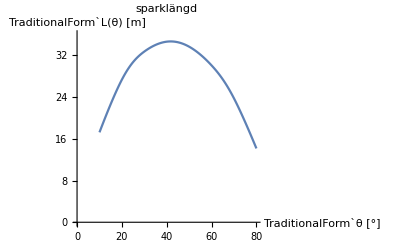

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

Using the same logic as earlier, all permutations beginning with a vote for B will “hit the x axis”,
All permutations where the first elements added equals 0 (B represents -1, A represents 1) will also hit the x-axis.

```mathematica
e1=Join @@@ Tuples[{Permutations[{B}],Permutations[{A,A,A,A,A,A,A,A,A,B,B,B,B}]}];
e2=Join @@@ Tuples[{Permutations[{A,B}],Permutations[{A,A,A,A,A,A,A,A,B,B,B,B}]}];
e3=Join @@@ Tuples[{Permutations[{A,A,B,B}],Permutations[{A,A,A,A,A,A,A,B,B,B}]}];
e4=Join @@@ Tuples[{Permutations[{A,A,A,B,B,B}],Permutations[{A,A,A,A,A,A,B,B}]}];
e5=Join @@@ Tuples[{Permutations[{A,A,A,A,B,B,B,B}],Permutations[{A,A,A,A,A,B}]}];
e6=Join @@@ Tuples[{Permutations[{A,A,A,A,A,B,B,B,B,B}],Permutations[{A,A,A,A}]}];
e =Union[e1,e2,e3,e4,e5,e6];
es = Binomial[14,9]-Length[e]
```

572